```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../FA_models/SMS-stop-FA/SMS-stop-FA_CT",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs}];
```

## g-g- t- t (1-loop - self energy)

The choice below for the momenta and the ordering of the particles in the process is equivalent to the correct
ordering for computing the effective vertex for the UFO format:
0 →4, with {} →{-F[9],F[9],V[4],V[4]} and all the momenta set as outgoing ({} → {p1,p2,p3,p4}).
However the choice below produces nicer diagrams.

```mathematica
topsCT = CreateCTTopologies[1,2->2,ExcludeTopologies->{WFCorrectionCTs,TadpoleCTs,BoxCTs,TriangleCTs}];
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,WFCorrections}];
processGGT = { V[4],V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[Join[topsCT,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
```

generic model {Lorentz} initialized

classes model {../../FA_models/SMS-stop-FA/SMS-stop-FA_CT} initialized

in total: 59 Particles insertions

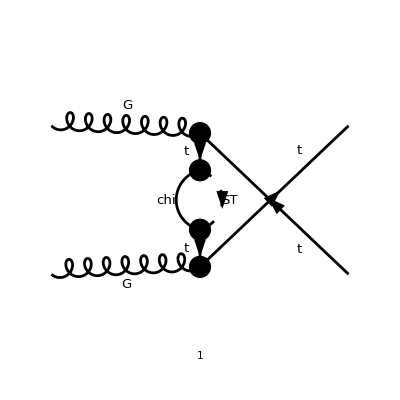

```mathematica
goodDiags=DiagramExtract[allDiags,{58}];
Paint[goodDiags,ColumnsXRows->{4,1},ImageSize->{ 600,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{pb,pa},LorentzIndexNames->{b,a},OutgoingMomenta->{p+pa,k2},LoopMomenta->{q},SUNIndexNames->{cc3,cc4,aa,bb},SUNFIndexNames->{c2,c1},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs,deltaCTL->0,deltaCTR->0}
```

in total: 1 Particles amplitude

(yDM^2 (ⅈ gs γ^a.(γ̄)^6 T_Col3Col5^cc4+ⅈ gs γ^a.(γ̄)^7 T_Col3Col5^cc4).(MT+γ·p).(γ̄)^7.(mChi+γ·q).(γ̄)^6.(MT+γ·p).(ⅈ gs γ^b.(γ̄)^6 T_Col5Col4^cc3+ⅈ gs γ^b.(γ̄)^7 T_Col5Col4^cc3))/((p^2-MT^2)^2 (q^2-mChi^2).((q-p)^2-mST^2))

```mathematica
(* 1/(2 p^2) ((mChi^2-mST^2+p^3)B0 -A0(mChi^2)+A0(mST^2)) = -B1(p^2) *)
```

```mathematica
ampC =FullSimplify[DiracSimplify[FeynAmpDenominatorExplicit[( TID[ampA,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True])]]]
```

-(ⅈ π^2 gs^2 yDM^2 T_Col5Col4^cc3 T_Col3Col5^cc4 (MT^2 γ^a.(γ·p).γ^b.(γ̄)^7+p^2 (MT (γ^a.γ^b.(γ̄)^6+γ^a.γ^b.(γ̄)^7)+γ^a.(γ·p).γ^b.(γ̄)^6)) ((mChi^2-mST^2+p^2) B_0(p^2,mChi^2,mST^2)-A_0(mChi^2)+A_0(mST^2)))/(2 p^2 (MT^2-p^2)^2)